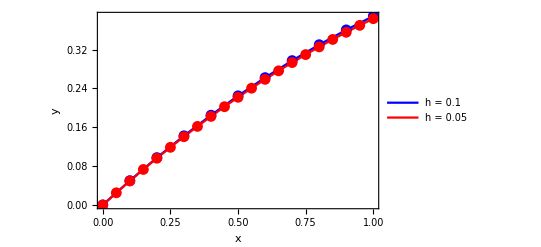

```mathematica
f[x_,y_]:=Cos[y]/(x+2)-0.3 y^2;
h1=0.1;
h2=0.05;

eulerCosh[f_,x0_,y0_,h_,n_]:=Module[{x,y,values},values={{x0,y0}};
x=x0;
y=y0;
Do[
y=y+h*f[x,y];
x=x+h;
AppendTo[values,{x,y}],{i,n}];
values]

solution1=eulerCosh[f,0,0,h1,Round[(1-0)/h1]];
solution2=eulerCosh[f,0,0,h2,Round[(1-0)/h2]];

ListLinePlot[{solution1,solution2},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{"x","y"},
Mesh->All,PlotLegends->Placed[{"h = 0.1","h = 0.05"},{0.8,0.5}]]
```

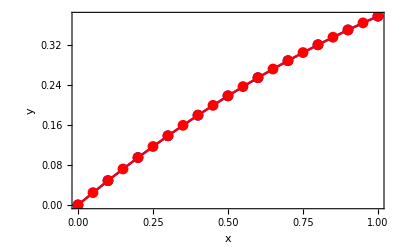

```mathematica
f[x_,y_]:=Cos[y]/(x+2)-0.3 y^2;
h1=0.1;
h2=0.05;

rungeKutta[f_,x0_,y0_,h_,n_]:=Module[{x,y,k1,k2,k3,k4,values},values={{x0,y0}};
x=x0;
y=y0;
Do[
k1=h*f[x,y];
k2=h*f[x+h/2,y+k1/2];
k3=h*f[x+h/2,y+k2/2];
k4=h*f[x+h,y+k3];
y=y+(k1+2 k2+2 k3+k4)/6;
x=x+h;
AppendTo[values,{x,y}],{i,n}];
values]

solution1=rungeKutta[f,0,0,h1,Round[(1-0)/h1]];
solution2=rungeKutta[f,0,0,h2,Round[(1-0)/h2]];

Show[ListLinePlot[solution1,PlotStyle->Blue,Frame->True,FrameLabel->{"x","y"},Mesh->All,PlotLegends->Placed[{"h=0.1"},{0.8,0.5}]],ListLinePlot[solution2,PlotStyle->Red,Frame->True,FrameLabel->{"x","y"},Mesh->All,PlotLegends->Placed[{"h=0.05"},{0.8,0.5}]]]
```

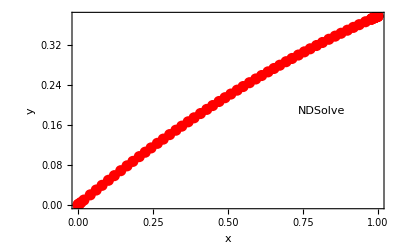

```mathematica
f[x_,y_]:=Cos[y]/(x+2)-0.3 y^2;

solNDSolve=NDSolve[{y'[x]==f[x,y[x]],y[0]==0},y,{x,0,1}];

Plot[Evaluate[y[x]/. solNDSolve],{x,0,1},PlotStyle->Red,Frame->True,FrameLabel->{"x","y"},
Mesh->All,MeshStyle->PointSize[0.02],PlotLegends->Placed["NDSolve",{0.8,0.5}]]
```

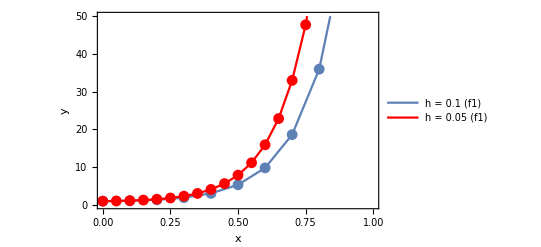

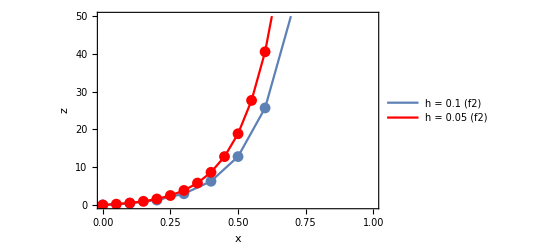

```mathematica
f1[x_,y_,z_]:=y+3*z+2*x;
f2[x_,y_,z_]:=4*y+7*z;

eulerMethod[x0_,y0_,z0_,h_,n_,f1_,f2_]:=Module[
{x=x0,y=y0,z=z0,points={{x0,y0,z0}}},Do[y=y+h*f1[x,y,z];
z=z+h*f2[x,y,z];
x=x+h;
AppendTo[points,{x,y,z}],{n}];
points]

solution1=eulerMethod[0,1,0,0.1,10,f1,f2];

solution2=eulerMethod[0,1,0,0.05,20,f1,f2];

Show[ListLinePlot[solution1[[All,{1,2}]],PlotLegends->{"h = 0.1 (f1)"},Frame->True,FrameLabel->{"x","y"},Mesh->All,PlotRange->{0,50}],ListLinePlot[solution2[[All,{1,2}]],PlotLegends->{"h = 0.05 (f1)"},Frame->True,FrameLabel->{"x","y"},PlotStyle->Red,Mesh->All,PlotRange->{0,50}]]

Show[ListLinePlot[solution1[[All,{1,3}]],PlotLegends->{"h = 0.1 (f2)"},Frame->True,FrameLabel->{"x","z"},Mesh->All,PlotRange->{0,50}],ListLinePlot[solution2[[All,{1,3}]],PlotLegends->{"h = 0.05 (f2)"},Frame->True,FrameLabel->{"x","z"},PlotStyle->Red,Mesh->All,PlotRange->{0,50}]]
```

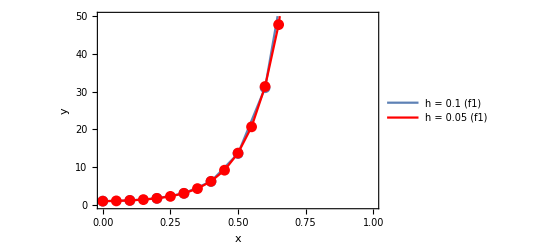

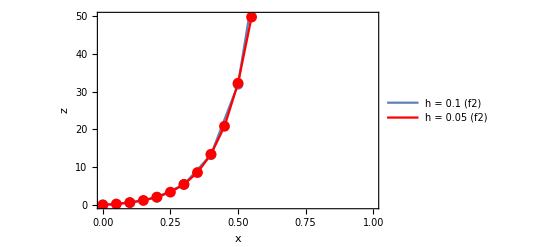

```mathematica
f1[x_,y_,z_]:=y+3 z+2 x;
f2[x_,y_,z_]:=4 y+7 z;

rungeKuttaMethod[x0_,y0_,z0_,h_,n_,f1_,f2_]:=Module[{
x=x0,y=y0,z=z0,
points={{x0,y0,z0}}},
Do[
k1y=h*f1[x,y,z];
k1z=h*f2[x,y,z];
k2y=h*f1[x+h/2,y+k1y/2,z+k1z/2];
k2z=h*f2[x+h/2,y+k1y/2,z+k1z/2];
k3y=h*f1[x+h/2,y+k2y/2,z+k2z/2];
k3z=h*f2[x+h/2,y+k2y/2,z+k2z/2];
k4y=h*f1[x+h,y+k3y,z+k3z];
k4z=h*f2[x+h,y+k3y,z+k3z];
y=y+(k1y+2*k2y+2*k3y+k4y)/6;
z=z+(k1z+2*k2z+2*k3z+k4z)/6;
x=x+h;
AppendTo[points,{x,y,z}],{n}];
points]

solution1=rungeKuttaMethod[0,1,0,0.1,10,f1,f2];

solution2=rungeKuttaMethod[0,1,0,0.05,20,f1,f2];

Show[ListLinePlot[solution1[[All,{1,2}]],PlotLegends->{"h = 0.1 (f1)"},PlotRange->{0,50},Frame->True,FrameLabel->{"x","y"},Mesh->All],
ListLinePlot[solution2[[All,{1,2}]],PlotLegends->{"h = 0.05 (f1)"},PlotRange->{0,50},PlotStyle->Red,Mesh->All],Frame->True,FrameLabel->{"x","y"}]

Show[ListLinePlot[solution1[[All,{1,3}]],PlotLegends->{"h = 0.1 (f2)"},PlotRange->{0,50},Mesh->All],
ListLinePlot[solution2[[All,{1,3}]],PlotLegends->{"h = 0.05 (f2)"},PlotRange->{0,50},PlotStyle->Red,Mesh->All],Frame->True,FrameLabel->{"x","z"}]
```

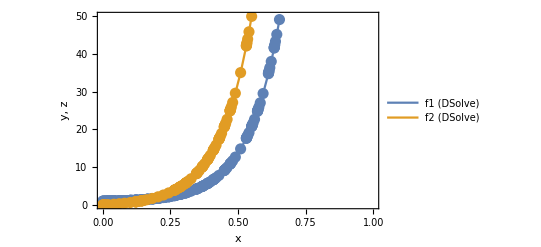

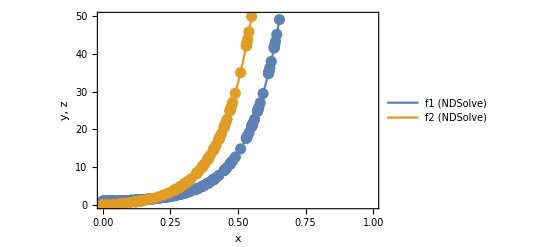

```mathematica
f1[x_,y_,z_]:=y+3 z+2 x;
f2[x_,y_,z_]:=4 y+7 z;

solDSolve=DSolve[{y'[x]==f1[x,y[x],z[x]],z'[x]==f2[x,y[x],z[x]],y[0]==1,z[0]==0},{y[x],z[x]},x];

solNDSolve=NDSolve[{y'[x]==f1[x,y[x],z[x]],z'[x]==f2[x,y[x],z[x]],y[0]==1,z[0]==0},{y,z},{x,0,1}];

Plot[Evaluate[{y[x],z[x]}/. solDSolve],{x,0,1},PlotLegends->{"f1 (DSolve)","f2 (DSolve)"},Frame->True,FrameLabel->{"x","y, z"},
PlotRange->{0,50},Mesh->All,MeshStyle->PointSize[0.02]]

Plot[Evaluate[{y[x],z[x]}/. solNDSolve],{x,0,1},PlotLegends->{"f1 (NDSolve)","f2 (NDSolve)"},Frame->True,FrameLabel->{"x","y, z"},
PlotRange->{0,50},Mesh->All,MeshStyle->PointSize[0.02]]
```